```mathematica
X={{1, 2}, {1, 4},{1,5}, {1,1},{1,9}, {1, 22}, {1,11}};
Y={1, 1,0,0,0, 1,0};
θ={θ1, θ2}
```

{θ1,θ2}

```mathematica
X[[1]] . θ
```

θ1+2 θ2

```mathematica
h[x_]:= 1/(1+Exp[-x]);
```

```mathematica
J =Simplify[Sum[-Y[[a]] Log[h[X[[a]].θ]] - (1-Y[[a]])Log[1-h[X[[a]].θ]], {a, 1, Length[X]}]]
```

-Log[1/(1+ⅇ^(-θ1-22 θ2))]-Log[1/(1+ⅇ^(-θ1-4 θ2))]-Log[1/(1+ⅇ^(-θ1-2 θ2))]-Log[1/(1+ⅇ^(θ1+θ2))]-Log[1/(1+ⅇ^(θ1+5 θ2))]-Log[1/(1+ⅇ^(θ1+9 θ2))]-Log[1/(1+ⅇ^(θ1+11 θ2))]

```mathematica
Plot3D[J,{θ1, -100, 100}, {θ2, -5, 5}]
```

-Graphics3D-

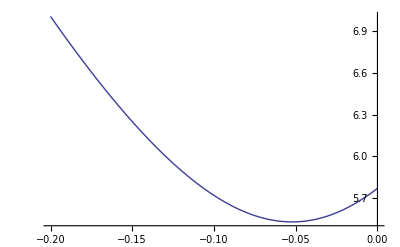

```mathematica
Plot[J/.{θ1->0.78434}, {θ2, -1/5, 0}]
```

```mathematica
eqs = {Simplify[D[J, θ1]]==0,Simplify[D[J, θ2]]==0}
```

{ⅇ^(θ1+θ2)/(1+ⅇ^(θ1+θ2))-1/(1+ⅇ^(θ1+2 θ2))-1/(1+ⅇ^(θ1+4 θ2))+ⅇ^(θ1+5 θ2)/(1+ⅇ^(θ1+5 θ2))+ⅇ^(θ1+9 θ2)/(1+ⅇ^(θ1+9 θ2))+ⅇ^(θ1+11 θ2)/(1+ⅇ^(θ1+11 θ2))-1/(1+ⅇ^(θ1+22 θ2))==0,ⅇ^(θ1+θ2)/(1+ⅇ^(θ1+θ2))-2/(1+ⅇ^(θ1+2 θ2))-4/(1+ⅇ^(θ1+4 θ2))+(5 ⅇ^(θ1+5 θ2))/(1+ⅇ^(θ1+5 θ2))+(9 ⅇ^(θ1+9 θ2))/(1+ⅇ^(θ1+9 θ2))+(11 ⅇ^(θ1+11 θ2))/(1+ⅇ^(θ1+11 θ2))-22/(1+ⅇ^(θ1+22 θ2))==0}

```mathematica
NSolve[eqs, θ]
```

$Aborted

```mathematica
min =NMinimize[J, θ]
```

{4.62754,{θ1→-0.784943,θ2→0.0636997}}

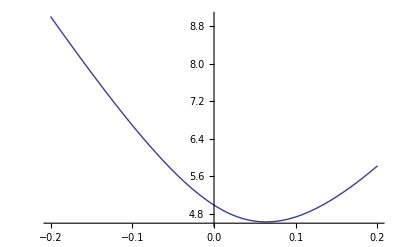

```mathematica
Plot[J/.min[[2,1]], {θ2, -1/5, 1/5}]
```